Part::pkspec1: The expression n cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

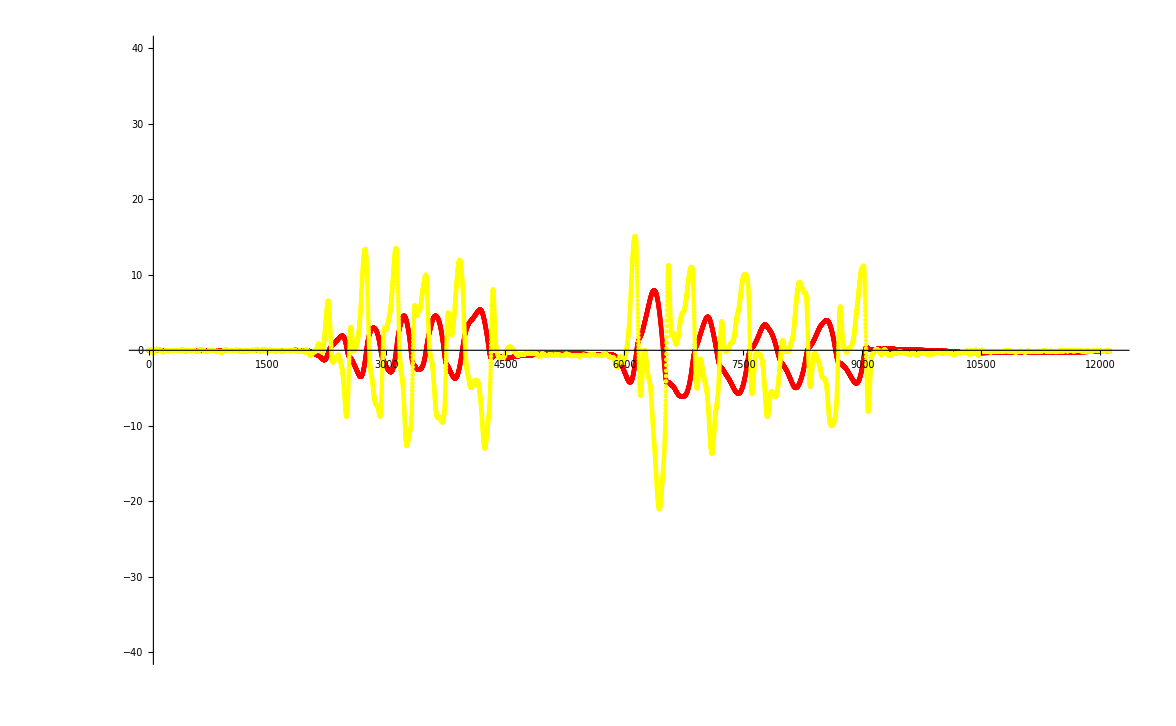

```mathematica
data =Import[FileNameJoin[{NotebookDirectory[],"log"}],"Table","FieldSeparators"->" "];
SetOptions[ListPlot,ImageSize->Large];
<<Quaternions`
accelX[n_]:=data[[n,1]];
accelY[n_]:=data[[n,2]];
accelZ[n_]:=data[[n,3]];
gyroX[n_]:=data[[n,4]];
gyroY[n_]:=data[[n,5]];
gyroZ[n_]:=data[[n,6]];
normAccel[n_]:=Normalize[{data[[n,1]],data[[n,2]],data[[n,3]]}];

complementaryRoll[coeff_]:=RecurrenceTable[{
euler[n+1]==coeff*(euler[n]+gyroY[n]*0.001)+(1-coeff)*(ArcTan[accelZ[n],accelY[n]]/Degree),
euler[1]==0},
euler,{n,1,Length[data]}];

mahonyRoll2[kp_,ki_,deltat_]:=Module[{Kp=kp,Ki=ki,deltaT=deltat,quaternion=Quaternion[1,0,0,0],errorIntegral={0,0,0},mahonyRoll={}},

Do[{
gyroRad={gyroX[n]Degree,gyroY[n]Degree,gyroZ[n]Degree};

v={
2*(quaternion[[2]]*quaternion[[4]]-quaternion[[1]]*quaternion[[3]]),2*(quaternion[[1]]*quaternion[[2]]+quaternion[[3]]*quaternion[[4]]),
quaternion[[1]]^2-quaternion[[2]]^2-quaternion[[3]]^2+quaternion[[4]]^2
};

error=Cross[normAccel[n],v];

errorIntegral=If[Ki >0,errorIntegral+error*deltaT,{0,0,0}];
gyroRad=gyroRad+Kp*error+Ki*errorIntegral;

qi=Quaternion[
-quaternion[[2]]*gyroRad[[1]]-quaternion[[3]]*gyroRad[[2]]-quaternion[[4]]*gyroRad[[3]],
+quaternion[[1]]*gyroRad[[1]]+quaternion[[3]]*gyroRad[[3]]-quaternion[[4]]*gyroRad[[2]],
+quaternion[[1]]*gyroRad[[2]]-quaternion[[2]]*gyroRad[[3]]+quaternion[[4]]*gyroRad[[1]],
+quaternion[[1]]*gyroRad[[3]]+quaternion[[2]]*gyroRad[[2]]-quaternion[[3]]*gyroRad[[1]]
];
qi=qi*0.5*deltaT;

quaternion=quaternion+qi;

quaternion=Normalize[quaternion];

t0=2*(quaternion[[1]]*quaternion[[2]]+quaternion[[3]]*quaternion[[4]]);
t1=1-2*(quaternion[[2]]^2+quaternion[[3]]^2);

mahonyRoll=Append[mahonyRoll,ArcTan[t1,t0]/Degree];

},{n,1,Length[data]}];mahonyRoll]

ListPlot[{mahonyRoll2[1,0,0.001],complementaryRoll[0.9](*,mahonyRoll2[10,0,0.001],,complementaryRoll[0.0000001]*)},PlotStyle->{Red,Yellow(*,Green,Blue*)},PlotRange->{{1,Length[data]},{-40,40}}]
```